## Results

```mathematica
SetDirectory[NotebookDirectory[] <> "/results"];
```

## N(τ_0)

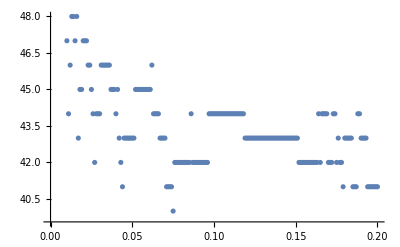

```mathematica
data:=Import["initstep_n.dat"]
ListPlot[data]
```

## N(fac)

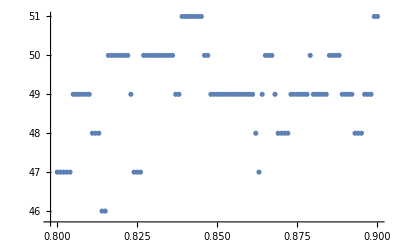

```mathematica
data:=Import["fac_n.dat"]
ListPlot[data]
```

## N(facmax)

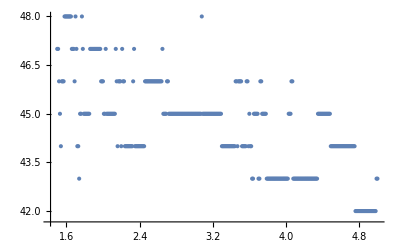

```mathematica
data:=Import["facmax_n.dat"]
ListPlot[data]
```

## N(facmin)

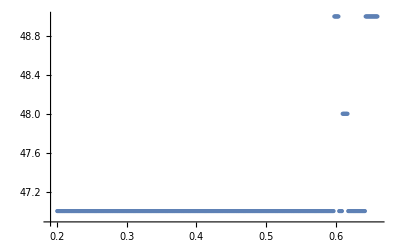

```mathematica
data:=Import["facmin_n.dat"]
ListPlot[data]
```

## N_rej(τ_0)

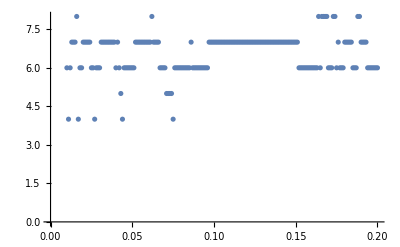

```mathematica
data:=Import["initstep_nrej.dat"]
ListPlot[data]
```

## N_rej(fac)

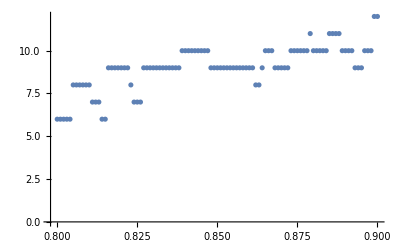

```mathematica
data:=Import["fac_nrej.dat"]
ListPlot[data]
```

## N_rej(facmax)

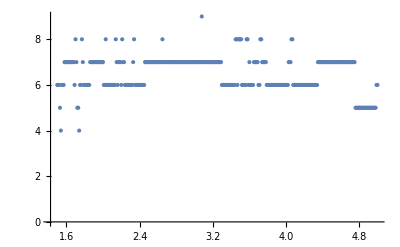

```mathematica
data:=Import["facmax_nrej.dat"]
ListPlot[data]
```

## N_rej(facmin)

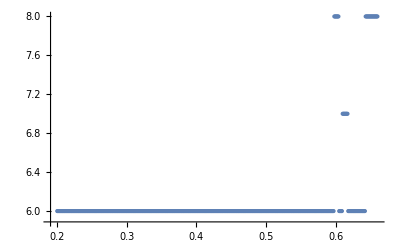

```mathematica
data:=Import["facmin_nrej.dat"]
ListPlot[data]
```

## T(τ_0)

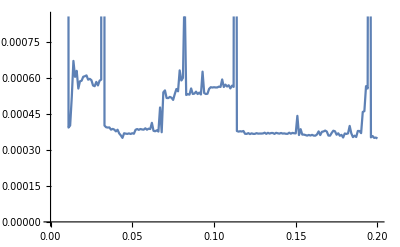

```mathematica
data:=Import["initstep_time.dat"]
ListLinePlot[data]
```

## T(fac)

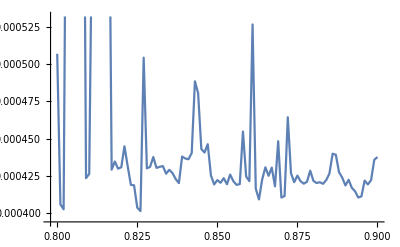

```mathematica
data:=Import["fac_time.dat"]
ListLinePlot[data]
```

## T(facmax)

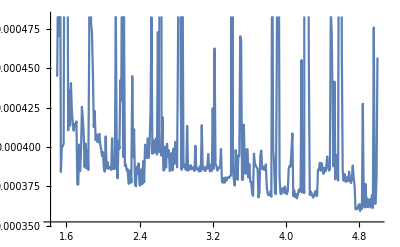

```mathematica
data:=Import["facmax_time.dat"]
ListLinePlot[data]
```

## T(facmin)

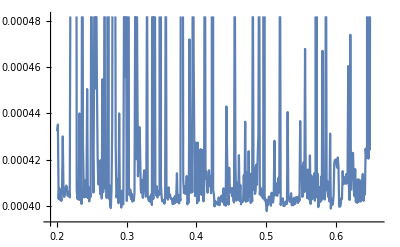

```mathematica
data:=Import["facmin_time.dat"]
ListLinePlot[data]
```

## ϵ(τ_0)

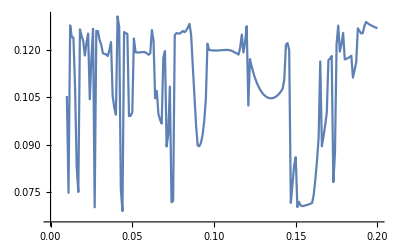

```mathematica
data:=Import["initstep_err.dat"]
ListLinePlot[data]
```

## ϵ(fac)

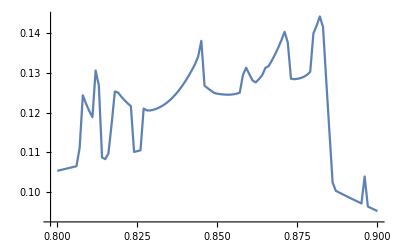

```mathematica
data:=Import["fac_err.dat"]
ListLinePlot[data]
```

## ϵ(facmax)

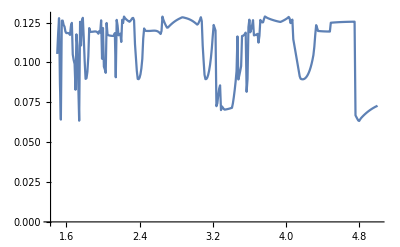

```mathematica
data:=Import["facmax_err.dat"]
ListLinePlot[data]
```

## ϵ(facmin)

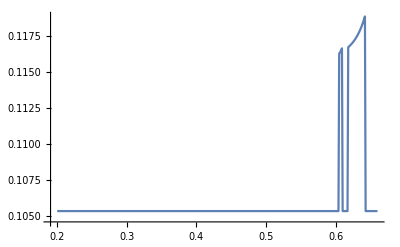

```mathematica
data:=Import["facmin_err.dat"]
ListLinePlot[data]
```

## Algorithm monitoring

Ensure that files in “monitoring” contain information about method you want (since it have same names both for Runge - Kutta and Dormand - Prince methods.

```mathematica
SetDirectory[NotebookDirectory[] <> "/monitoring"];
```

## Runge - Kutta

### Global error

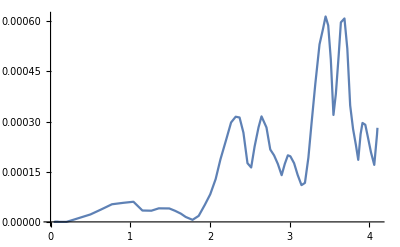

```mathematica
data:= Import["global_err.dat"]
ListLinePlot[data]
```

### Local error

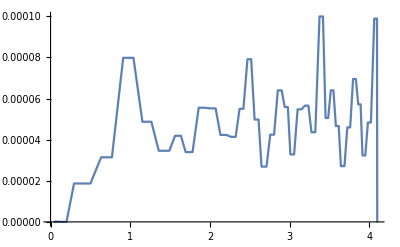

```mathematica
data:= Import["local_err.dat"]
ListLinePlot[data]
```

### Steps

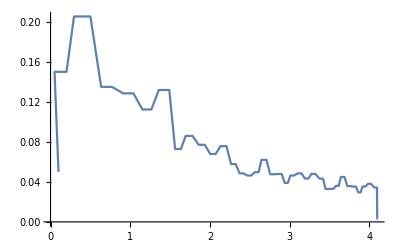

```mathematica
data:= Import["steps.dat"]
ListLinePlot[data]
```

### Values

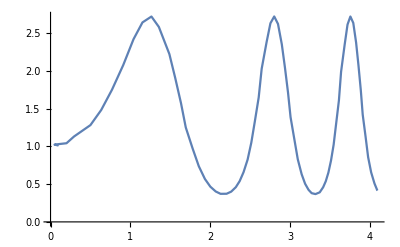

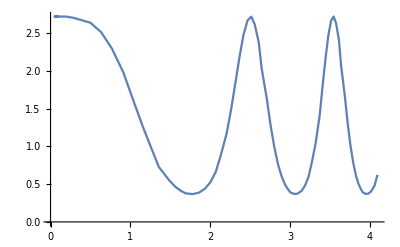

```mathematica
data:= Import["vals.dat"]
y1={};
y2={};
For[i=1,i<Length[data],i++,
AppendTo[y1, {data⟦i⟧⟦1⟧, data⟦i⟧⟦2⟧}];
AppendTo[y2, {data⟦i⟧⟦1⟧, data⟦i⟧⟦3⟧}];
]
ListLinePlot[y1]
ListLinePlot[y2]
```

## Dormand - Prince

### Global error

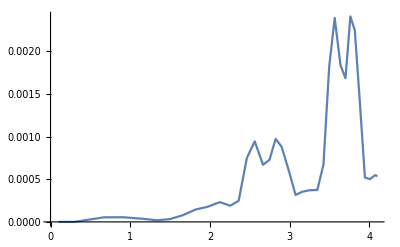

```mathematica
data:= Import["global_err.dat"]
ListLinePlot[data]
```

#### Local error

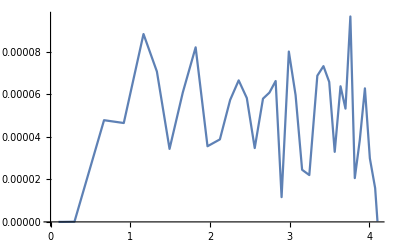

```mathematica
data:= Import["local_err.dat"]
ListLinePlot[data]
```

### Steps

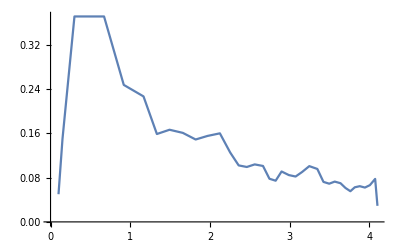

```mathematica
data:= Import["steps.dat"]
ListLinePlot[data]
```

#### Values

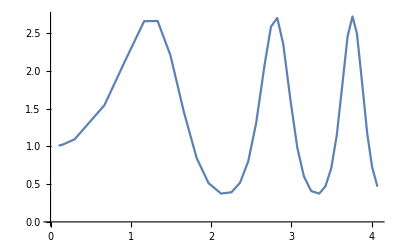

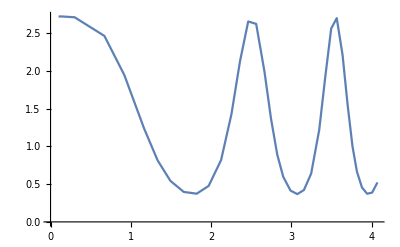

```mathematica
data:= Import["vals.dat"]
y1={};
y2={};
For[i=1,i<Length[data],i++,
AppendTo[y1, {data⟦i⟧⟦1⟧, data⟦i⟧⟦2⟧}];
AppendTo[y2, {data⟦i⟧⟦1⟧, data⟦i⟧⟦3⟧}];
]
ListLinePlot[y1]
ListLinePlot[y2]
```